```mathematica
<<PhysicalApplications`Astrophysics`GravitationalWaves`Detectors`Miscellaneous`;
```

```mathematica
h1[Mc_,f_]:=Mc^(5/3) f^(2/3) (1-UnitStep[f-1/Mc])
h2[Mc_,f_]:=Mc^(5/3) f^(2/3)DetectorCumulativeAngleFactorGreater["MonteCarlo"][Mc f]UnitStep[1-Mc f]
PDFm[Mc_,z_]:=1/Mc(*obviously fake PDF, just a placeholder*)
h1PDFm[Mc_,z_,f_]:=h1[Mc,f]PDFm[Mc,z]
h2PDFm[Mc_,z_,f_]:=h2[Mc,f]PDFm[Mc,z]
```

```mathematica
H1[f_,z_]:=NIntegrate[h1PDFm[Mc,z,f],{Mc,10,50}]
H2[f_,z_]:=NIntegrate[h2PDFm[Mc,z,f],{Mc,10,50}]
```

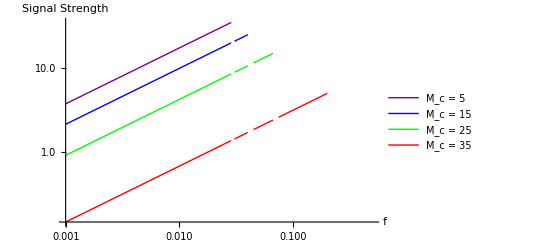

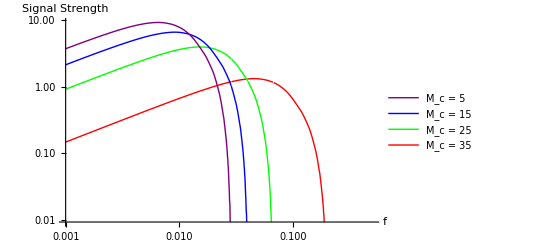

```mathematica
LogLogPlot[{h1[5,f],h1[15,f],h1[25,f],h1[35,f]},{f,.001,.5},AxesLabel->{Style["f",Black,Bold,20],Style["Signal Strength",Black,Bold,20]},TicksStyle->12,ImageSize->400,PlotRangePadding->.5,PlotStyle->{Red,Green,Blue,Purple},PlotLegends->Placed[LineLegend[{Purple,Blue,Green,Red},{Style["M_c = 5",Black,Bold,15],Style["M_c = 15",Black,Bold,15],Style["M_c = 25",Black,Bold,15],Style["M_c = 35",Black,Bold,15]}],{0.85,0.325}]]

LogLogPlot[{h2[5,f],h2[15,f],h2[25,f],h2[35,f]},{f,.001,.5},AxesLabel->{Style["f",Black,Bold,20],Style["Signal Strength",Black,Bold,20]},TicksStyle->12,ImageSize->400,PlotRangePadding->.5,PlotStyle->{Red,Green,Blue,Purple},PlotLegends->Placed[LineLegend[{Purple,Blue,Green,Red},{Style["M_c = 5",Black,Bold,15],Style["M_c = 15",Black,Bold,15],Style["M_c = 25",Black,Bold,15],Style["M_c = 35",Black,Bold,15]}],{0.875,0.775}]]
```

NIntegrate::inumr: The integrand f^2/3\ Mc^2/3\ (1 - UnitStep[f - 1/Mc]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{5, 50}}.

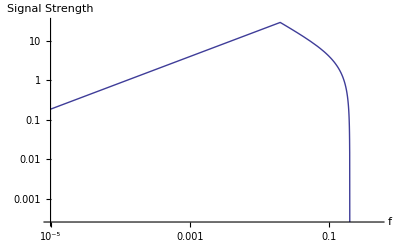

NIntegrate::inumr: The integrand f has evaluated to non-numerical values for all sampling points in the region with boundaries {{5, 50}}.

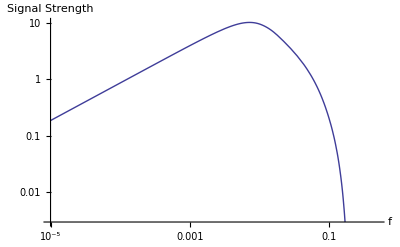

```mathematica
LogLogPlot[NIntegrate[h1PDFm[Mc,1,f],{Mc,5,50}],{f,.00001,.5},AxesLabel->{Style["f",Black,Bold,15],Style["Signal Strength",Black,Bold,15]},TicksStyle->15]
LogLogPlot[NIntegrate[h2PDFm[Mc,1,f],{Mc,5,50}],{f,.00001,.5},AxesLabel->{Style["f",Black,Bold,15],Style["Signal Strength",Black,Bold,15]},TicksStyle->15]
```